```mathematica
x1=-2;
x2=-2.99;
x3=1;
a0=1;
a1=0;
a2=1;
a3=2.9979;
A=Table[0,{x,4},{y,4}];
A[[1,1]]=-2*a0*x3;
A[[1,2]]=0;
A[[1,3]]=a0*x1+a1*x3;
A[[1,4]]=a0*x2-a2*x3;
A[[2,1]]=0;
A[[2,2]]=-2*a0*x3;
A[[2,3]]=a0*x2+a2*x3;
A[[2,4]]=-a0*x1+a1*x3;
A[[3,1]]=a0*x1+a1*x3;
A[[3,2]]=a0*x2+a2*x3;
A[[3,3]]=-a1*x1-a2*x2+1/(2*x3)*(a3*x3^2-a0*x1^2-a0*x2^2);
A[[3,4]]=a2*x1-a1*x2;
A[[4,1]]=a0*x2-a2*x3;
A[[4,2]]=-a0*x1+a1*x3;
A[[4,3]]=a2*x1-a1*x2;
A[[4,4]]=a1*x1+a2*x2+1/(2*x3)*(a3*x3^2-a0*x1^2-a0*x2^2);
A
```

{{-2,0,-2,-3.99},{0,-2,-1.99,2},{-2,-1.99,-1.9811,-2.},{-3.99,2,-2.,-7.9611}}

```mathematica
q1=-2*a0*x3
q2=2*a0*x1
q3=2*a0*x2
q4=2*a1*x3
q5=2*a2*x3
q6=2*(a2*x1-a1*x2)
q7=-(a1*x1+a2*x2)
q8=1/(2*x3)*(a3*x3^2-a0*x1^2-a0*x2^2)
```

-2

-4

-5.98

0

2

-4.

2.99

-4.9711

```mathematica
l1=0;
l2=1;
l3=3;
a0=1;
a1=2;
a2=3;
B=Table[0,{x,4},{y,4}];
B[[1,1]]=0;
B[[1,2]]=0;
B[[1,3]]=a0*l1;
B[[1,4]]=a0*l2;
B[[2,1]]=0;
B[[2,2]]=0;
B[[2,3]]=a0*l2;
B[[2,4]]=-a0*l1;
B[[3,1]]=a0*l1;
B[[3,2]]=a0*l2;
B[[3,3]]=-(a1*l1+a2*l2)+a0*l3;
B[[3,4]]=(a2*l1-a1*l2);
B[[4,1]]=a0*l2;
B[[4,2]]=-a0*l1;
B[[4,3]]=(a2*l1-a1*l2);
B[[4,4]]=(a1*l1+a2*l2)+a0*l3;
B
```

{{0,0,0,1},{0,0,1,0},{0,1,0,-2},{1,0,-2,6}}

```mathematica
q1=0
q2=2*a0*l1
q3=2*a0*l2
q4=0
q5=0
q6=-2*a1*l2+2*a2*l1
q7=-a1*l1-a2*l2
q8=a0*l3
```

0

0

2

0

0

-4

-3

3

```mathematica
myplot=ContourPlot3D[{A[[1, 1]]*x^2 + (A[[1, 2]] + A[[2, 1]])*x*y + (A[[1, 3]] + A[[3, 1]])*x*z + (A[[1, 4]] + A[[4, 1]])*x + A[[2, 2]]*y^2 + (A[[2, 3]] + A[[3, 2]])*y*z + (A[[2, 4]] + A[[4, 2]])*y + A[[3, 3]]*z^2 + (A[[3, 4]] + A[[4, 3]])*z + A[[4, 4]] == 0, B[[1, 1]]*x^2 + (B[[1, 2]] + B[[2, 1]])*x*y + (B[[1, 3]] + B[[3, 1]])*x*z + (B[[1, 4]] + B[[4, 1]])*x + B[[2, 2]]*y^2 + (B[[2, 3]] + B[[3, 2]])*y*z + (B[[2, 4]] + B[[4, 2]])*y + B[[3, 3]]*z^2 + (B[[3, 4]] + B[[4, 3]])*z + B[[4, 4]] == 0}, {x, -10, 10}, {y, -10, 10}, {z, -10, 10}, PerformanceGoal -> "Quality", MeshStyle -> Gray, Mesh -> 0, Boxed -> False, Axes -> True, AxesLabel -> {X, Y, Z}, MaxRecursion -> 15, PlotPoints -> 50, PlotRange -> Automatic, ContourStyle -> {{Orange, Opacity[0.5]}, {Magenta,Opacity[0.5]}}];
Show[myplot]
```

-Graphics3D-

```mathematica
eigenvalues=Eigenvalues[A];
eigenvectors=Eigenvectors[A];
transformatrix=Transpose[{eigenvectors[[4]],eigenvectors[[3]],eigenvectors[[2]], eigenvectors[[1]]}];
```

```mathematica
afterA=Transpose[transformatrix].A.transformatrix;
MatrixForm[afterA]
```

(0.36564 | -2.70617×10^-16 | -2.43555×10^-15 | 2.10942×10^-15
-2.77556×10^-16 | 0.929103 | -8.25728×10^-16 | 3.88578×10^-16
-2.44249×10^-15 | -6.10623×10^-16 | -4.30297 | 2.55351×10^-15
2.66454×10^-15 | 4.44089×10^-16 | 2.88658×10^-15 | -10.934)

```mathematica
afterB=Transpose[transformatrix].B.transformatrix;
MatrixForm[afterB]
```

(0.240976 | 0.939025 | 0.492638 | 1.29949
0.939025 | 0.0808091 | 0.902847 | 2.73402
0.492638 | 0.902847 | 1.53757 | 1.76353
1.29949 | 2.73402 | 1.76353 | 4.14064)

```mathematica
Clear[V];Clear[u];Clear[v];
V={(u+afterA[[1,1]]*v)/afterA[[1,1]], (u*v-afterA[[2,2]])/afterA[[2,2]], (u-afterA[[1,1]]*v)/Sqrt[-afterA[[1,1]]*afterA[[3,3]]], (u*v+afterA[[2,2]])/Sqrt[-afterA[[2,2]]*afterA[[4,4]]]};
```

```mathematica
goalformula=Collect[Expand[V.afterB.V], {u^2, u}]
```

-1.16129-0.893782 v+0.0844193 v^2+u (-3.68421+1.18689 v+1.94767 v^2)+u^2 (4.92802+10.19 v+2.34769 v^2)

```mathematica
delta=Expand[(-3.6842133575981753+1.186888197136455 v+1.9476729284654533 v^2)^2-4*(4.928024913912981+10.19004757803993 v+2.3476945315542057 v^2)*(-1.1612942840418379-0.8937820575934281 v+0.08441926811046771 v^2)];
```

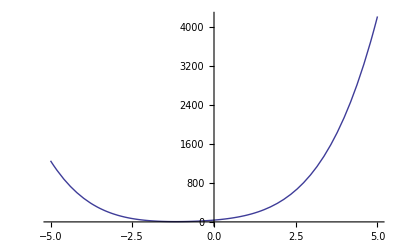

```mathematica
Plot[delta, {v,-5, 5}]
```

```mathematica
Solve[delta==0, v]
```

{{v→-1.18866-0.499464 ⅈ},{v→-1.18866+0.499464 ⅈ},{v→-0.406937-2.67294 ⅈ},{v→-0.406937+2.67294 ⅈ}}

```mathematica
u1=(-(-3.6842133575981753+1.186888197136455 v+1.9476729284654533 v^2)+Sqrt[delta])/(2*(4.928024913912981+10.19004757803993 v+2.3476945315542057 v^2));
u2=(-(-3.6842133575981753+1.186888197136455 v+1.9476729284654533 v^2)-Sqrt[delta])/(2*(4.928024913912981+10.19004757803993 v+2.3476945315542057 v^2));
```

```mathematica
afterP1={(u1+afterA[[1,1]]*v)/afterA[[1,1]], (u1*v-afterA[[2,2]])/afterA[[2,2]], (u1-afterA[[1,1]]*v)/Sqrt[-afterA[[1,1]]*afterA[[3,3]]], (u1*v+afterA[[2,2]])/Sqrt[-afterA[[2,2]]*afterA[[4,4]]]};
afterP2={(u2+afterA[[1,1]]*v)/afterA[[1,1]], (u2*v-afterA[[2,2]])/afterA[[2,2]], (u2-afterA[[1,1]]*v)/Sqrt[-afterA[[1,1]]*afterA[[3,3]]], (u2*v+afterA[[2,2]])/Sqrt[-afterA[[2,2]]*afterA[[4,4]]]};
```

```mathematica
P1=transformatrix.afterP1;
P2=transformatrix.afterP2;
```

```mathematica
Branch1=Graphics3D[{PointSize[0.011],Black,Point[Table[{P1[[1]]/P1[[4]],P1[[2]]/P1[[4]],P1[[3]]/P1[[4]]},{v,-25, 25, 0.005}]]}, Boxed -> False, Axes -> True, AxesLabel -> {X, Y, Z}];
Branch2=Graphics3D[{PointSize[0.011],Black,Point[Table[{P2[[1]]/P2[[4]],P2[[2]]/P2[[4]],P2[[3]]/P2[[4]]},{v,-4.6,1.3, 0.005}]]}];
Show[Branch1, Branch2, myplot]
```

-Graphics3D-

```mathematica
afterP1
```

{2.73493 (0.36564 v+(3.68421-1.18689 v-1.94767 v^2+√(36.465+56.2074 v+32.7295 v^2+9.5757 v^3+3.00067 v^4))/(2 (4.92802+10.19 v+2.34769 v^2))),1.07631 (-0.929103+(v (3.68421-1.18689 v-1.94767 v^2+√(36.465+56.2074 v+32.7295 v^2+9.5757 v^3+3.00067 v^4)))/(2 (4.92802+10.19 v+2.34769 v^2))),0.79724 (-0.36564 v+(3.68421-1.18689 v-1.94767 v^2+√(36.465+56.2074 v+32.7295 v^2+9.5757 v^3+3.00067 v^4))/(2 (4.92802+10.19 v+2.34769 v^2))),0.313747 (0.929103+(v (3.68421-1.18689 v-1.94767 v^2+√(36.465+56.2074 v+32.7295 v^2+9.5757 v^3+3.00067 v^4)))/(2 (4.92802+10.19 v+2.34769 v^2)))}